```mathematica
Quit[]
```

```mathematica
λ=ⅈ 1;
σ=ⅈ 1;
γ=-1;
```

```mathematica
Subscript[λ, 0]=Re[λ];
Subscript[λ, 1]=Im[λ];
Subscript[σ, 0]=Re[σ];
Subscript[σ, 1]=Im[σ];
Subscript[γ, 0]=Re[γ];
Subscript[γ, 1]=Im[γ];
```

```mathematica
ϕ=0;
solutions=Solve[{
β Subscript[ρ, 1]==Subscript[λ, 1] Subscript[ρ, 1]+Subscript[σ, 1] Subscript[ρ, 1]^3+Subscript[γ, 1] 1/(2 π) Subscript[ρ, 1] α+Subscript[γ, 1] Subscript[ρ, 2] (2 π-α) 1/(2 π) Cos[ϕ]+Subscript[ρ, 2] (2 π-α) 1/(2 π) Subscript[γ, 0] Sin[ϕ],
0==Subscript[λ, 0] Subscript[ρ, 1]+Subscript[σ, 0] Subscript[ρ, 1]^3+Subscript[γ, 0] 1/(2 π) Subscript[ρ, 1] α+Subscript[ρ, 2] (2 π-α) 1/(2 π) Subscript[γ, 0] Cos[ϕ]-Subscript[γ, 1] Subscript[ρ, 2] (2 π-α) 1/(2 π) Sin[ϕ],
Subscript[ρ, 2] β Cos[ϕ]==Subscript[λ, 0] Subscript[ρ, 2] Sin[ϕ]+Subscript[λ, 1] Subscript[ρ, 2] Cos[ϕ]+Subscript[σ, 0] Subscript[ρ, 2]^3 Sin[ϕ]+Subscript[σ, 1] Subscript[ρ, 2]^3 Cos[ϕ]+1/(2 π) Subscript[γ, 1] Subscript[ρ, 1] α+1/(2 π) Subscript[γ, 0] Subscript[ρ, 2] (2 π-α) Sin[ϕ]+1/(2 π) Subscript[γ, 1] (2 π-α) Subscript[ρ, 2] Cos[ϕ],
-Subscript[ρ, 2] β Sin[ϕ]==Subscript[λ, 0] Subscript[ρ, 2] Cos[ϕ]-Subscript[λ, 1] Subscript[ρ, 2] Sin[ϕ]+Subscript[σ, 0] Subscript[ρ, 2]^3 Cos[ϕ]-Subscript[σ, 1] Subscript[ρ, 2]^3 Sin[ϕ]+1/(2 π) Subscript[γ, 0] Subscript[ρ, 1] α+1/(2 π) Subscript[γ, 0] Subscript[ρ, 2] (2 π-α) Cos[ϕ]-1/(2 π) Subscript[γ, 1] (2 π-α) Subscript[ρ, 2] Sin[ϕ]
}, {Subscript[ρ, 1],Subscript[ρ, 2],α,β}];
(* Print["До замены свободных переменный"]; *)
solutions;
(* Print["После замены свободных переменных"]; *)
Do [
findFlag=MemberQ[solutions[[index]],Subscript[ρ, 1]->_];
If[! findFlag,solutions[[index]]=solutions[[index]]/.Subscript[ρ, 1]->1;
AppendTo[solutions[[index]],Subscript[ρ, 1]->1]];
findFlag=MemberQ[solutions[[index]],Subscript[ρ, 2]->_];
If[! findFlag,solutions[[index]]=solutions[[index]]/.Subscript[ρ, 2]->1;AppendTo[solutions[[index]],Subscript[ρ, 2]->1]];
findFlag=MemberQ[solutions[[index]],α->_];
If[! findFlag,solutions[[index]]=solutions[[index]]/.α->1;AppendTo[solutions[[index]],α->1]];
findFlag=MemberQ[solutions[[index]],β->_];
If[! findFlag,solutions[[index]]=solutions[[index]]/.β->1;AppendTo[solutions[[index]],β->1]],
{index,1,Length[solutions]}
]
solutions
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ρ_1→0,ρ_2→0,α→1,β→1},{ρ_2→0,α→0,β→2,ρ_1→1},{ρ_1→0,α→2 π,β→2,ρ_2→1},{ρ_1→0,ρ_2→0,β→1,α→1},{ρ_1→-1,α→π,β→2,ρ_2→1},{ρ_1→0,ρ_2→0,β→1,α→1}}

Проверка

```mathematica
Do[
Print[{β Subscript[ρ, 1]==Subscript[λ, 1] Subscript[ρ, 1]+Subscript[σ, 1] Subscript[ρ, 1]^3+Subscript[γ, 1] 1/(2 π) Subscript[ρ, 1] α+Subscript[γ, 1] Subscript[ρ, 2] (2 π-α) 1/(2 π) Cos[ϕ]+Subscript[ρ, 2] (2 π-α) 1/(2 π) Subscript[γ, 0] Sin[ϕ],
0==Subscript[λ, 0] Subscript[ρ, 1]+Subscript[σ, 0] Subscript[ρ, 1]^3+Subscript[γ, 0] 1/(2 π) Subscript[ρ, 1] α+Subscript[ρ, 2] (2 π-α) 1/(2 π) Subscript[γ, 0] Cos[ϕ]-Subscript[γ, 1] Subscript[ρ, 2] (2 π-α) 1/(2 π) Sin[ϕ],
Subscript[ρ, 2] β Cos[ϕ]==Subscript[λ, 0] Subscript[ρ, 2] Sin[ϕ]+Subscript[λ, 1] Subscript[ρ, 2] Cos[ϕ]+Subscript[σ, 0] Subscript[ρ, 2]^3 Sin[ϕ]+Subscript[σ, 1] Subscript[ρ, 2]^3 Cos[ϕ]+1/(2 π) Subscript[γ, 1] Subscript[ρ, 1] α+1/(2 π) Subscript[γ, 0] Subscript[ρ, 2] (2 π-α) Sin[ϕ]+1/(2 π) Subscript[γ, 1] (2 π-α) Subscript[ρ, 2] Cos[ϕ],
-Subscript[ρ, 2] β Sin[ϕ]==Subscript[λ, 0] Subscript[ρ, 2] Cos[ϕ]-Subscript[λ, 1] Subscript[ρ, 2] Sin[ϕ]+Subscript[σ, 0] Subscript[ρ, 2]^3 Cos[ϕ]-Subscript[σ, 1] Subscript[ρ, 2]^3 Sin[ϕ]+1/(2 π) Subscript[γ, 0] Subscript[ρ, 1] α+1/(2 π) Subscript[γ, 0] Subscript[ρ, 2] (2 π-α) Cos[ϕ]-1/(2 π) Subscript[γ, 1] (2 π-α) Subscript[ρ, 2] Sin[ϕ]}/.solutions[[index]]],
{index,Length[solutions]}
]
```

{True,True,True,True}

{True,True,True,True}

{True,True,True,True}

«3 more identical outputs»

```mathematica
Clear[ρ1,ρ2,α,β];
choosenSolution=solutions[[5]]
{ρ1,ρ2,α,β}={Subscript[ρ, 1],Subscript[ρ, 2],α,β}/.choosenSolution;
ρ[x_,ϕ_]:=Piecewise[{
{ρ1,x<=α},
{ρ2 ⅇ^(ⅈ ϕ),x>α}
}]
ξ[τ_,x_,ϕ_]:=ρ[x,ϕ] ⅇ^(ⅈ β τ)
Subscript[ξ, 1][τ_,x_,ϕ_]:=Re[ξ[τ,x,ϕ]]
x1=5.5;
x2=2;
T=100;
Subscript[ξ, 1][1,x1,ϕ];
ϕ;
```

{ρ_1→-1,α→π,β→2,ρ_2→1}

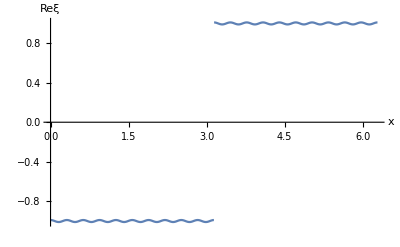

```mathematica
Plot[{Subscript[ξ, 1][0,x,ϕ]+Cos[20x]/100},{x,0,2 Pi},AxesLabel->{"x","Reξ"}]
```

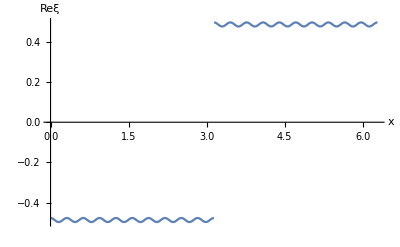

```mathematica
Plot[{Subscript[ξ, 1][T,x,ϕ]+Cos[20x]/100},{x,0,2 Pi},AxesLabel->{"x","Reξ"}]
```

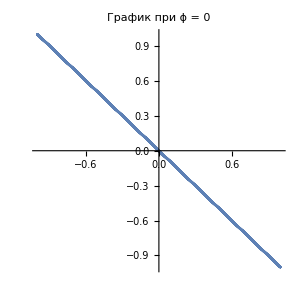

```mathematica
ParametricPlot[{Subscript[ξ, 1][τ,x1,ϕ],Subscript[ξ, 1][τ,x2,ϕ]},{τ,0,T},PlotRange->All,PlotLabel->"График при ϕ = " <> ToString[ϕ,StandardForm]]
```